SimulationTools > Grid Functions

# Grid Functions

SimulationTools provides an interface to grid-based data from numerical simulations.  It is currently capable of reading HDF5 files produced by Carpet and returns variables as DataRegion objects.

## Common Arguments

Most of the functions in this package take at least three arguments: sim, var and dims.

sim | The name of the simulation containing the data to read
var | The name of the grid variable
dims | The dimensions to be read.These can be given either as a list of numbers of coordinate names ({1,2,3} or {“x”,”y”,”z”}) or asa combined string “xyz”.

Common arguments to gridfunction functions.

The following options can be given:

Iteration | 0 | The iteration to read
Map | None | The map to read (use None for single map data, or an integer for multi-map)
RefinementLevel | 0 | The refinement level to read.
TimeLevel | 0 | The time level to read
Variable | First in file | The variable to read

Common options to gridfunction functions.

## Functions

### ReadGridFunction[sim, var, dims]

Read a grid function for the variable var of dimension dims in sim and return it as a DataRegion.

This function reads a variable from a simulation and returns it as a single DataRegion object. 
1D, 2D and 3D variables are currently supported.  If the file is part of a multi-file set, all the files will be used to read the variable.

If there is more than one component (i.e. the data is split into separate parts corresponding to different processors), the components will all be read and joined together into a single rectangular DataRegion.  If the union of the components is not rectangular, the smallest rectangular region surrounding all components will be used, and points not in any component will take the value None.

If the file appears in more than one segment of a multi-segment simulation, the correct segment for the given iteration will be located automatically.  In addition to the common options listed above, the following option can be given:

StripGhostZones | True | Remove inter-processor ghost zones from the data

### ReadIterations[sim, var, dims]

Read the iteration numbers present in sim for var. If the options Map, RefinementLevel, TimeLevel or Variable are specified, then only iterations corresponding to those will be included.

### ReadMaps[sim, var, dims]

Read the maps present in sim for var.  If the options Iteration, RefinementLevel, TimeLevel or Variable are specified, then only iterations corresponding to those will be included.

### ReadRefinementLevels[sim, var, dims]

Read the refinement levels present in sim for var. If the options Iteration, Map, TimeLevel or Variable are specified, then only iterations corresponding to those will be included.

### ReadTimeLevels[sim, var, dims]

Read the timelevels present in sim for var. If the options Iteration, Map, RefinementLevel or Variable are specified, then only iterations corresponding to those will be included.

### FindGridFunctions[sim]

Read the names of variables for which gridfunction data is available in sim.

### ReadGridFunctionDimensions[sim]

Read the available dimensions of a gridfunction in sim.

## Example

Examine the variable phi from the simulation bbh in the x-y plane.

```mathematica
ReadIterations["bbh","phi","xy"]//Short
```

{0,1024,2048,3072,4096,5120,«7»,13312,14336,15360,16384,17408,18432}

```mathematica
ReadRefinementLevels["bbh","phi","xy"]
```

{0,1,2,3,4,5,6}

```mathematica
ReadMaps["bbh","phi","xy"]
```

{None}

```mathematica
ReadTimeLevels["bbh","phi","xy"]
```

{0}

```mathematica
phi=ReadGridFunction["bbh","phi","xy",Iteration->4096,RefinementLevel->3]
```

DataRegion[ML_BSSN::phi.01,<47,87>,{{-0.75,10.75},{-10.75,10.75}}]

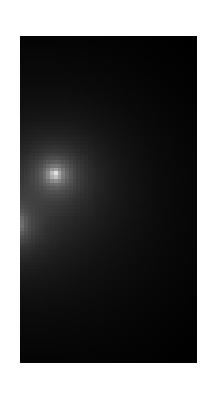

```mathematica
ArrayPlot[phi]
```

RELATED TUTORIALS

DataRegion

NumericalRelativity